```mathematica
(*Thesis Project RSSI, SNR Values*)
```

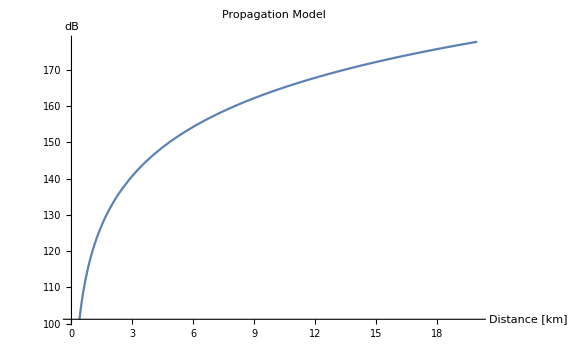

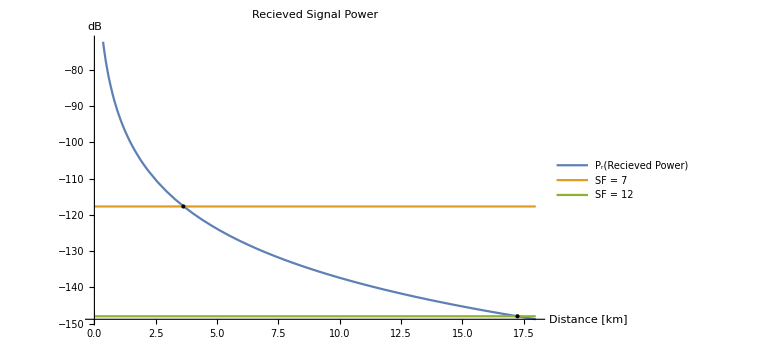

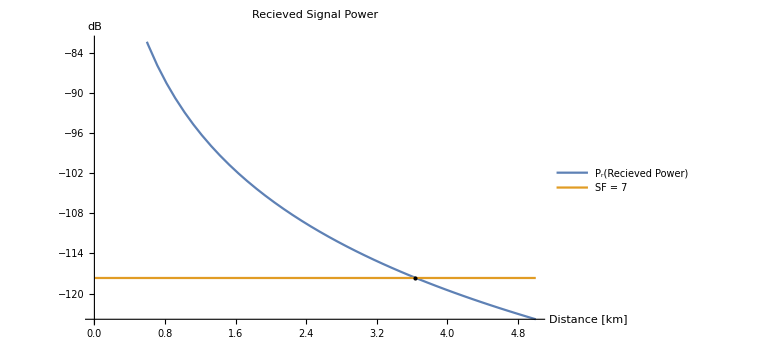

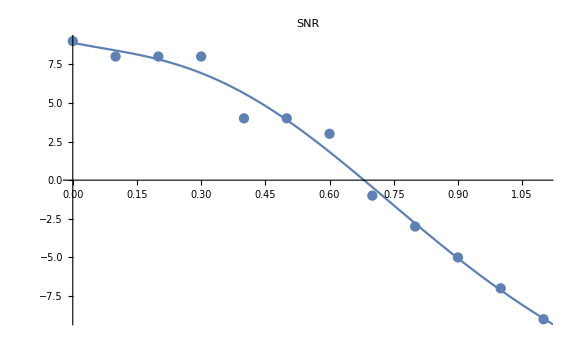

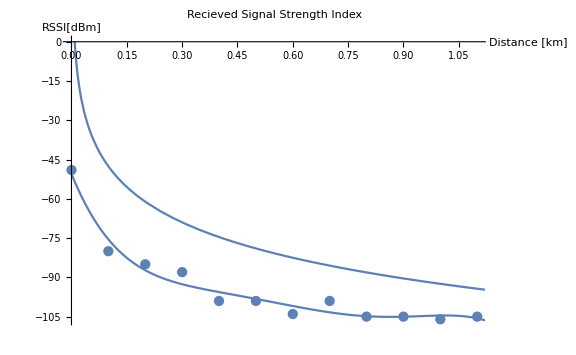

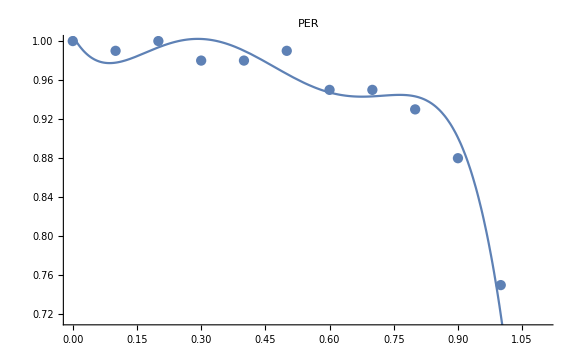

```mathematica
(*Hata model Open area*)
(*http://citeseerx.ist.psu.edu/viewdoc/download?doi=10.1.1.303.4057&rep=rep1&type=pdf*)
ClearAll["Global`*"]
Subscript[h, b]=Subscript[h, m]=1;
f =868.1;
Subscript[Pt, W]=100*10^-3;
Subscript[Pt, dBm]=10*Log10[Subscript[Pt, W]]+30;
Subscript[Pt, dBw]=10*Log10[Subscript[Pt, W]];
Subscript[Gt, dBi]=Subscript[Gr, dBi]=3.43;

dist = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1};
prssi={-49,-80,-85,-88,-99,-99,-104,-99,-105,-105,-106,-105};
(*snr={9,8,8,8,4,5,-1,5,-3,-5,-7,-9};*)
snr1 ={9,8,8,8,4,4,3,-1,-3,-5,-7,-9}; (**)
(*totPacket = {100/100,99/100,100/100,98/100,98/100,100/100,88/100,100/100,75/100,95/100,93/100,23/100};*)
totPacket1 = {100/100,99/100,100/100,98/100,98/100,99/100,95/100,95/100,93/100,88/100,75/100,23/100};(**)
rssi =Transpose[{dist,prssi}];
per=Transpose[{dist,totPacket1}];
snr = Transpose[{dist,snr1}];
paraSNR = Fit[snr,{1,kx,kx^2,kx^3,kx^4,kx^5},kx];
paraRSSI= Fit[rssi,{1,kx,kx^2,kx^3,kx^4,kx^5},kx];
paraPER= Fit[per,{1,1,kx,kx^2,kx^3,kx^4,kx^5},kx];

BW=125000;
k=1.38*10^-23;
T=290;
x[h_]:=(1.1*Log10[f]-0.7)*h-(1.56*Log10[f]-0.8);
a=69.55+26.161*Log10[f]-13.82*Log10[Subscript[h, b]]-x[Subscript[h, m]];
b=44.9-6.55*Log10[Subscript[h, b]];
c=40.94+4.78*(Log10[f])^2-18.33*Log10[f];
Ltotal[d_]:=a+b*Log10[d]-c;

Subscript[Pr, dBm][d_]:=Subscript[Pt, dBm]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-Ltotal[d];
Subscript[Pr, dBw][d_]:=Subscript[Pt, dBw]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-Ltotal[d];

intersection1={d,-117.67}/.NSolve[Subscript[Pr, dBm][d]==-117.6,d];
intersection2={d,-148}/.NSolve[Subscript[Pr, dBm][d]==-148,d];

Plot[Ltotal[d],{d,0,20},AxesLabel->{"Distance [km]","dB"},PlotLabel->"Propagation Model",ImageSize->Large]

Plot[{Subscript[Pr, dBm][d],-117.67,-148},{d,0,18},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1],Point[intersection2]},PlotLabel-> "Recieved Signal Power",PlotLegends->{"P_r(Recieved Power)","SF = 7", "SF = 12"}]

Plot[{Subscript[Pr, dBm][d],-117.67},{d,0,5},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1]},PlotLabel-> "Recieved Signal Power",PlotLegends->{"P_r(Recieved Power)","SF = 7"}]

Show[ListPlot[snr],Plot[paraSNR,{kx,0,1.2}],PlotLabel-> "SNR",ImageSize->Large]
Show[ListPlot[rssi],Plot[paraRSSI,{kx,0,1.2}],
Plot[{Subscript[Pr, dBm][d],-117.67,-148},{d,0,1.7}],
ImageSize->Large,
AxesLabel->{"Distance [km]","RSSI[dBm]"},
PlotLabel-> "Recieved Signal Strength Index"
]
Show[ListPlot[per],Plot[paraPER,{kx,0,1.2}],PlotLabel-> "PER",ImageSize->Large]
```

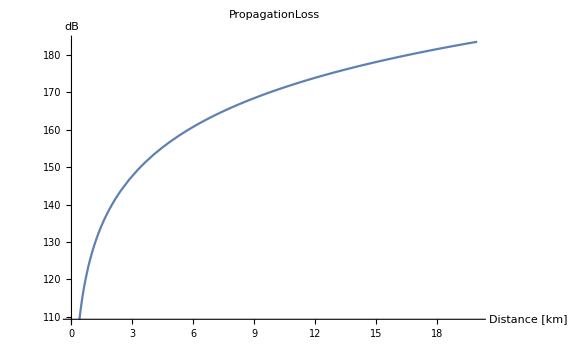

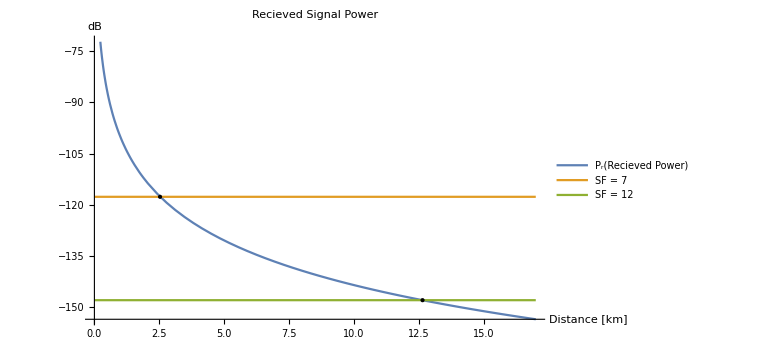

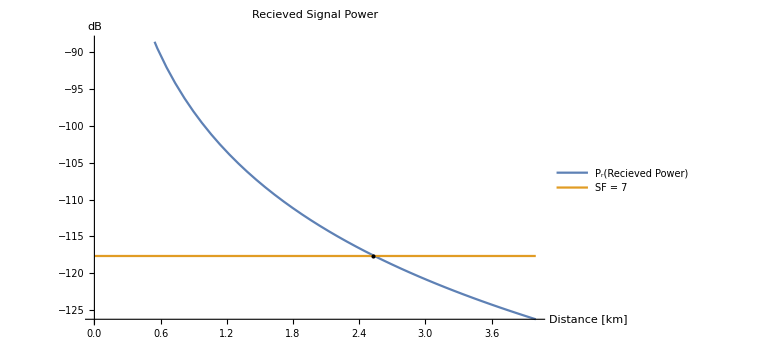

-Graphics-

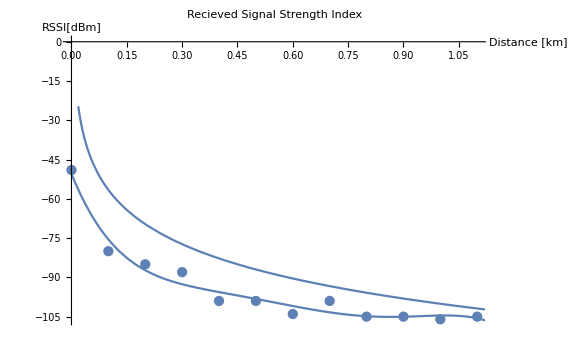

-Graphics-

```mathematica
ClearAll["Global`*"]
Subscript[h, b]=Subscript[h, m]=1;
f =868.1;
Subscript[Pt, W]=100*10^-3;
Subscript[Pt, dBm]=10*Log10[Subscript[Pt, W]/10^-3];
Subscript[Pt, dBw]=10*Log10[Subscript[Pt, W]];
Subscript[Gt, dBi]=Subscript[Gr, dBi]=3.43;

dist = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1};
prssi={-49,-80,-85,-88,-99,-99,-104,-99,-105,-105,-106,-105};
(*snr={9,8,8,8,4,5,-1,5,-3,-5,-7,-9};*)
snr1 ={9,8,8,8,4,4,3,-1,-3,-5,-7,-9}; (**)
(*totPacket = {100/100,99/100,100/100,98/100,98/100,100/100,88/100,100/100,75/100,95/100,93/100,23/100};*)
totPacket1 = {100/100,99/100,100/100,98/100,98/100,99/100,95/100,95/100,93/100,88/100,75/100,23/100};(**)
rssi =Transpose[{dist,prssi}];
per=Transpose[{dist,totPacket1}];
snr = Transpose[{dist,snr1}];
paraSNR = Fit[snr,{1,kx,kx^2,kx^3,kx^4,kx^5},kx];
paraRSSI= Fit[rssi,{1,kx,kx^2,kx^3,kx^4,kx^5},kx];
paraPER= Fit[per,{1,1,kx,kx^2,kx^3,kx^4,kx^5},kx];

BW=125000;
k=1.38*10^-23;
T=290;
x=43.5;
Subscript[L, 0]=89;

Subscript[F, 1][h_]:=(h/30.48)^2;
Subscript[F, 2][G_]:=G/4;
Subscript[F, 3][h_]:=(h/3);
Subscript[F, 4][f_,n_]:=(f/900)^-n;
Subscript[F, 5][G_]:=G/1;
Subscript[F, 0]=Subscript[F, 1][1]*Subscript[F, 2][Subscript[Gr, dBi]-2.15]*Subscript[F, 3][1]*Subscript[F, 4][868.1,2.5]*Subscript[F, 5][Subscript[Gt, dBi]-2.15];
Ltotal[d_]:=Subscript[L, 0]+x*Log10[d]-10*Log10[Subscript[F, 0]];
Subscript[Pr, dBm][d_]:=Subscript[Pt, dBm]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-Ltotal[d];
Subscript[Pr, dBw][d_]:=Subscript[Pt, dBw]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-Ltotal[d];
intersection1={d,-117.67}/.NSolve[Subscript[Pr, dBm][d]==-117.6,d];
intersection2={d,-148}/.NSolve[Subscript[Pr, dBm][d]==-148,d];
Plot[Ltotal[d],{d,0,20},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,PlotLabel->"PropagationLoss"]

Plot[{Subscript[Pr, dBm][d],-117.67,-148},{d,0,17},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1],Point[intersection2]},PlotLabel-> "Recieved Signal Power",PlotLegends->{"P_r(Recieved Power)","SF = 7", "SF = 12"}]

Plot[{Subscript[Pr, dBm][d],-117.67},{d,0,4},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1]},PlotLabel-> "Recieved Signal Power",PlotLegends->{"P_r(Recieved Power)","SF = 7"}]

Show[ListPlot[snr],Plot[paraSNR,{kx,0,1.2}],PlotLabel-> "SNR",ImageSize->Large]
Show[ListPlot[rssi],Plot[paraRSSI,{kx,0,1.2}],
Plot[{Subscript[Pr, dBm][d],-117.67,-148},{d,0,1.7}],
ImageSize->Large,
AxesLabel->{"Distance [km]","RSSI[dBm]"},
PlotLabel-> "Recieved Signal Strength Index"
]
Show[ListPlot[per],Plot[paraPER,{kx,0,1.2}],PlotLabel-> "PER",ImageSize->Large]
```

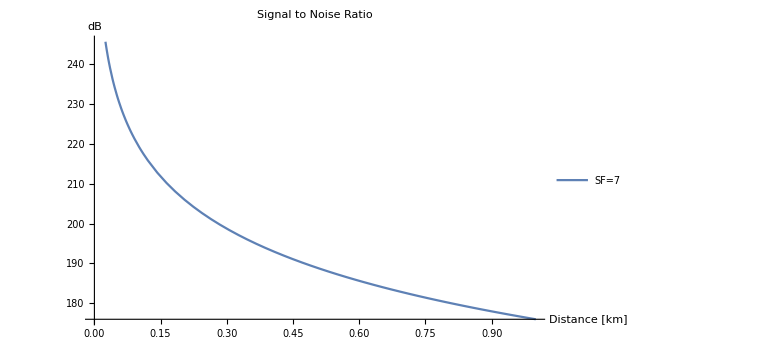

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*SNR*)
NF=10*Log10[k*BW*T];
Subscript[N, dBm]=-174+NF+10*Log10[BW];
SNR[SpreadFactor_,dist_] :=Subscript[Pr, dBm][dist]-Subscript[N, dBm];
Plot[{SNR[7,r]},{r,0,1.0},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,PlotLabel-> "Signal to Noise Ratio",PlotLegends->{"SF=7","SF = 8","SF = 9","SF = 10", "SF = 11" , "SF = 12"}]
```